```mathematica
R=8.314;
F=83500;
```

```mathematica
CVSimulationAlpha[length_,dimension_,density_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[position_]:=d*Total[Cases[distribution/@((position+#)&/@range)-distribution[position],_Real]];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]-=itemp;
If[distribution[electrodeposition]<0,distribution[electrodeposition]=0.];
];
distribution[#]+=Analyzer[#]&/@mesh;
];
i
];
```

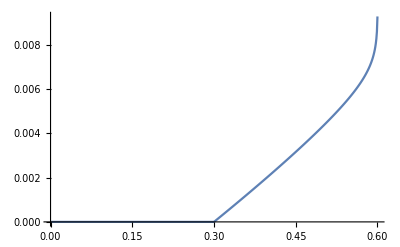

```mathematica
ListLinePlot@%
```

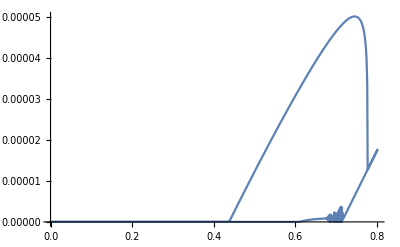

```mathematica
CVSimulationAlpha[100,1,0.01,0.3,1,300,5000,0.0001,{100},0.,0.,0.8,0.001,2];
ListLinePlot[%,PlotRange->All]
```

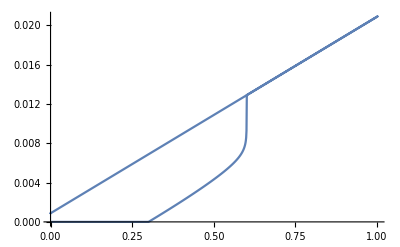

```mathematica
ListLinePlot@%
```

```mathematica
Analyzer[range_,d_,distribution_,position_]:=d*Total[Cases[distribution/@((position+#)&/@range)-distribution[position],_Real]];
```

```mathematica
Clear[A];
```

```mathematica
Table[A[{i,j}]=1,{i,1,10},{j,1,10}];
```

```mathematica
A[{1,2}]
```

1

```mathematica
Table[A[{i,j}]=1.,{i,1,10},{j,1,10}];
A[{5,5}]=0.;
```

```mathematica
A[{5,5}]
```

0

```mathematica
Select[Tuples[{-1,0,1},2],Total[#^2]==1&]+{{1,1}}
```

Thread::tdlen: Objects of unequal length in {{-1,0},{0,-1},{0,1},{1,0}}+{{1,1}} cannot be combined.

{{1,1}}+{{-1,0},{0,-1},{0,1},{1,0}}

```mathematica
(A[#]+=Analyzer[Select[Tuples[{-1,0,1},2],Total[#^2]==1&],0.1,A,#])&/@Flatten[Table[{i,j},{i,10},{j,10}],1]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.4,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Select[Tuples[{-1,0,1},2],Total[#^2]==1&]
```

{{-1,0},{0,-1},{0,1},{1,0}}

```mathematica
Flatten[Table[{i,j},{i,1,10},{j,1,10}],1]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}

```mathematica
CVSimulationBeta[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,reduced},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
(reduced[#]=reduceddensity)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[name_,position_]:=d*Total[Cases[name/@((position+#)&/@range)-name[position],_Real]];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition]]+8.314*T/n/F*Log[reduced[electrodeposition]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]-=itemp;
If[distribution[electrodeposition]<0,distribution[electrodeposition]=0.];
];
distribution[#]+=Analyzer[#]&/@mesh;
];
i
];
```

```mathematica
DSolve[D[c1[x,t],t]==-D1 D[c1[x,t],x,x]&&D[c2[x,t],t]==D2 D[c2[x,t],x,x]&&c1[0,t]/c2[0,t]==Exp[n F/R/T (a+w t)],{c1,c2},x,t]
```

DSolve[c1^(0,1)[x,t]==-D1 c1^(2,0)[x,t]&&c2^(0,1)[x,t]==D2 c2^(2,0)[x,t]&&c1[0,t]/c2[0,t]==ⅇ^((10043.3 n (a+t w))/T),{c1,c2},x,t]

```mathematica
First[c1/.NDSolve[D[c1[x,t],t]==D[c1[x,t],x,x]&&D[c2[x,t],t]== D[c2[x,t],x,x]&&1/(c1[0,t]/c2[0,t])==Exp[-0.5+ F/R/300 *0.005 t]&&c1[x,0]==0.001&&c2[x,0]==Exp[-0.5]*0.001,{c1,c2},{x,0,10},{t,0,10}]][x,t];
Plot[Evaluate[-(D[%,t]-D[%,x,x])*F/.x->0],{t,0,10},PlotRange->All]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::ndsz: At t == 3.94923, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
CVSimulationGamma[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,reduced,Balancer},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
(reduced[#]=reduceddensity)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[name_,position_]:=d*Total[Cases[name/@((position+#)&/@range)-name[position],_Real]];
Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position]-(1+Exp[-standardVolt+volt])^-1(reductant[position]+oxidant[position]))*n F;
oxidant[position]=(1+Exp[-standardVolt+volt])^-1(reductant[position]+oxidant[position]) ;
oxidant[position]=(1-(1+Exp[-standardVolt+volt])^-1)(reductant[position]+oxidant[position]) ;
current
];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}];
];
i
];
```

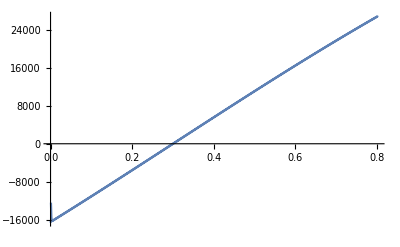

```mathematica
CVSimulationGamma[100,1,1,1,0.3,1,300,5000,0.0001,{{100}},0.,0.,0.8,0.001,2];
ListLinePlot[%,PlotRange->All]
```